# Fresnel Boundaries

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2019 Eugene d’Eon 
www.eugenedeon.com

## Non-polarized

## Reflection and Refraction

Helper functions to reflect and refract vectors:

```mathematica
refract[w_,n_,eta1_,eta2_]:=-eta1/eta2(w-(w.n)n)-(√(1-(eta1/eta2)^2(1-(w.n)^2)))n;
reflect[v_,n_]:=-v+2 n n.v;
```

## Dielectric Fresnel

Dielectric reflectance for incoming light with incoming cosine costhetai and ratio of internal to external indices of etaratio:

```mathematica
evalF[g_,c_]:=1/2(g-c)^2/(g+c)^2(1+(c(g+c)-1)^2/(c(g-c)+1)^2);
FR[etaratio_,costhetai_]:=If[
etaratio^2-1+costhetai^2≥0,
evalF[√(etaratio^2-1+costhetai^2),costhetai],
1]
```

### interactive Snell’s law explorer

```mathematica
Manipulate[
plotFresnel=Graphics[
{
Gray,
GrayLevel[.9],
Rectangle[{-1,-1},{1,0}],
Black,
Line[{{-1,0},{1,0}}],
{Dashed,
Arrow[{{0,0},{0,1}}]},
Arrow[{{-Sin[θi],Cos[θi]},{0,0}}],
Arrow[{{0,0},FR[ηt/ηi,Cos[θi]]{Sin[θi],Cos[θi]}}],
Arrow[{{0,0},(1-FR[ηt/ηi,Cos[θi]])refract[{-Sin[θi],Cos[θi]},{0,1},ηi,ηt]}],
Text["η_i",{.9,0.05}],
Text["η_t",{.9,-0.05}],
Text["F_R",1.2FR[ηt/ηi,Cos[θi]]{Sin[θi],Cos[θi]}],
Text["F_T",1.2(1-FR[ηt/ηi,Cos[θi]])refract[{-Sin[θi],Cos[θi]},{0,1},ηi,ηt]],
GrayLevel[.8],
Circle[{0,0},0.5,{Pi/2,Pi/2+θi}],
Black,
Text["θi",.55{-Sin[θi/2],Cos[θi/2]}]
}
],{ηi,1,2},{ηt,1,2},{θi,0,Pi/2}]
```

### Benchmark data

```mathematica
ns={5/10,7/10,9/10,99/100,101/100,11/10,14/10,2};
FRdata=Table[NumberForm[FR[n,Cos[t]],{8,8}],{n,ns},{t,{0.,0.2,0.5,1.,1.2,1.5}}];
Transpose[Join[{Table[N[n],{n,ns}]},Transpose[FRdata]]]//Grid
```

0.5 | 0.11111111 | 0.11175198 | 0.28326783 | 1 | 1 | 1
0.7 | 0.03114187 | 0.03124674 | 0.03870036 | 1 | 1 | 1
0.9 | 0.00277008 | 0.00277588 | 0.00309559 | 0.04529667 | 1 | 1
0.99 | 0.00002525 | 0.00002530 | 0.00002756 | 0.00018462 | 0.00132454 | 1
1.01 | 0.00002475 | 0.00002479 | 0.00002690 | 0.00016095 | 0.00096253 | 0.14322539
1.1 | 0.00226757 | 0.00227070 | 0.00242550 | 0.00987357 | 0.03762339 | 0.50722589
1.4 | 0.02777778 | 0.02779989 | 0.02881388 | 0.06118057 | 0.13573578 | 0.65791346
2. | 0.11111111 | 0.11114523 | 0.11262121 | 0.15018951 | 0.22278595 | 0.68340009

### Hemispherical Albedo - Smooth Dielectric

[Dunkle 1963, Ozisik 1973 p. 60]

```mathematica
DielectricHemisphericalAlbedo[n_]:=1/2+((n-1)(3n+1))/(6(n+1)^2)-(2 n^3(n^2+2n-1))/((n^2+1)(n^4-1))+(8 n^4(n^4+1))/((n^2+1)(n^4-1)^2)Log[n]+(n^2(n^2-1)^2)/((n^2+1)^3)Log[(n-1)/(n+1)]
```

Our approximation [Aug 2019] for  1 < η < 3:

```mathematica
DielectricHemisphericalAlbedoApprox[n_]:=Log[(10893 n-1438.2)/(1+10212 n-774.4 n^2)]
```

#### Error plot:

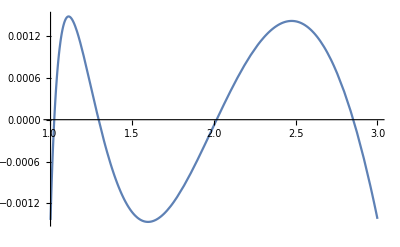

```mathematica
Plot[DielectricHemisphericalAlbedo[n]-DielectricHemisphericalAlbedoApprox[n],{n,1.003,3}]
```

### Hemispherical Albedo - Smooth Dielectric - Flatland

[Allen 1973]

```mathematica
DielectricHemisphericalAlbedoFlatland[n_]:=1/15 (-(2 (1+31 n^2+15 n^4+31 n^6+n^8) EllipticE[1/(1-n^2)])/((-1+n^2)^(3/2) (1+n^2)^2)+1/((-1+n^4)^3)((-1+n) (1+n) ((1+n^2) (7+24 n^2+102 n^4+10 n^6+15 n^8)+30 n^3 √(1+n^2) (2+n^2+2 n^4) ArcSinh[n])+2 n^2 √(-1+n^2) ((-22-15 n^2-47 n^4-n^6+9 n^8+n^10) EllipticK[1/(1-n^2)]+15 n^4 (2+n^2+2 n^4) EllipticPi[1+n^2,1/(1-n^2)])))
```

## Conductor Fresnel

### Exact

```mathematica
Clear[p,q,rhoPerp,rhoPar,Rs,Rp];
p[ni_,n_,k_,theta_]:=√(1/2(√((n^2-k^2-ni^2 Sin[theta]^2)^2+4 n^2 k^2)+(n^2-k^2-ni^2 Sin[theta]^2)));
q[ni_,n_,k_,theta_]:=√(1/2(√((n^2-k^2-ni^2 Sin[theta]^2)^2+4 n^2 k^2)-(n^2-k^2-ni^2 Sin[theta]^2)));
```

```mathematica
rhoPerp[p_,q_,n1_,t_]:=((n1 Cos[t]-p)^2+q^2)/((n1 Cos[t]+p)^2+q^2);
rhoPar[p_,q_,n1_,t_]:=((p-n1 Sin[t] Tan[t])^2+q^2)/((p+n1 Sin[t] Tan[t])^2+q^2)rhoPerp[p,q,n1,t]
```

```mathematica
FR[ni_,n_,k_,t_]:=1/2(rhoPerp[p[ni,n,k,t],q[ni,n,k,t],ni,t]+rhoPar[p[ni,n,k,t],q[ni,n,k,t],ni,t])
```

Reflectance at normal incidence:

```mathematica
ConductorNormalReflectance[ni_,n_,k_]:=1-(4 ni n)/((ni+n)^2+k^2)
```

#### modified Gulbrandsen mapping for ni = 1:

These two functions take F0 (r) and G tint parameter and map to n + i k:

```mathematica
nmaprG[r_,G_]:=(-1+(2-4 (1-Sin[(G π)/2]^2)) √r-r)/(-1+r)
```

```mathematica
kmaprG[r_,G_]:=√((-(-1+(-1-r+√r (2-4 (1-Sin[(G π)/2]^2)))/(-1+r))^2+r (1+(-1-r+√r (2-4 (1-Sin[(G π)/2]^2)))/(-1+r))^2)/(1-r))
```

These two functions find G from n + i k.   (r is ConductorNormalReflectance[1,n,k])

```mathematica
gmap[n_,k_]:=1-(-1-k^2+n^2+√((1+k^2)^2+2 (-1+k^2) n^2+n^4))/(2 √((1+k^2)^2+2 (-1+k^2) n^2+n^4))
```

```mathematica
Gmap[n_,k_]:=(2 ArcSin[√gmap[n,k]])/π
```

### Schlick’s Approximation

```mathematica
mix[a_,b_,t_]:=b t + (1-t) a;
FRSchlickFresnel[ni_,n_,k_,theta_]:=mix[
ConductorReflectance[ni,n,k],
1,
(1-Cos[theta])^5
]
```

### Additional approximate form

Mentioned in [Pharr and Humphreys - Physically Based Rendering], first edition, [9.1], [9.2] (more accurate for larger k).  See also [Dunkle 1963]

```mathematica
FRPharrHumphreys[n_,k_,t_]:=1/2(((n^2+k^2)Cos[t]^2-2 n Cos[t]+1)/((n^2+k^2)Cos[t]^2+2 n Cos[t]+1)+(((n^2+k^2)-2 n Cos[t]+Cos[t]^2)/((n^2+k^2)+2 n Cos[t]+Cos[t]^2)))
```

### Hemispherical Albedo - Smooth Conductor

#### approximation 1

[Dunkle 1963, Ozisik 1973 p. 60] - approximation, exact for PharrHumphreys approximate form:

(parallel and perpendicular integrals):

```mathematica
ConductorAlbedo1[n_,k_]:=1-(8n-8 n^2 Log[(1+2n+n^2+k^2)/(n^2+k^2)]+(8n(n^2-k^2))/k ArcTan[k/(n+n^2+k^2)])
```

```mathematica
ConductorAlbedo2[n_,k_]:=1-((8n)/(n^2+k^2)-(8 n^2)/((n^2+k^2)^2)Log[1+2n+n^2+k^2]+(8n(n^2-k^2))/(k(n^2+k^2)^2)ArcTan[k/(1+n)])
```

unpolarized average:

```mathematica
ConductorHemisphericalAlbedoApprox1[n_,k_]:=1/2(ConductorAlbedo1[n,k]+ConductorAlbedo2[n,k])
```

#### approximation 2

Our 1st approximation [Aug 2019] for  0.1 < η < 4, 1.7 < k < 8  - accurate to within about 0.001

```mathematica
ConductorHemisphericalAlbedoApprox2[n_,k_]:=(-8.214737476609672+(133.7359744765862-98.9832978804228 n) n+k (-182.3702003078492+(59.56171376011442-3.9828814738544107 n) n)+k^2 (-62.591907101534154+(-13.109290817253394+0.3081804514395202 n) n))/((-395.2681486337069-78.47602559071363 n) n+k (-187.16625841046798+(94.65173464738277-15.855805815946251 n) n)+k^2 (-62.07520207202666+n (-15.438703954274438+1. n)))
```

#### approximation 2

Our 2nd approximation [Aug 2019] for  0.1 < η < 4, 1.7 < k < 8  - accurate to within about 0.00006

```mathematica
rGfit[r_,G_]:=(-2.0451558353360357+14.9839211083631 G+1.3890774118488598 G^2+60.88405996107553 r+97.32802959940146 G r-145.19694441443767 G^2 r+322.2806535116558 r^2-687.9935126644131 G r^2+338.6486829760271 G^2 r^2)/(230.27759868799 G-198.15004297964407 G^2+512.5359759247783 r-1005.5551398186406 G r+470.70682665699746 G^2 r-127.45924551986035 r^2+191.70842828834142 G r^2-73.78542717613104 G^2 r^2)
```

```mathematica
ConductorHemisphericalAlbedoApprox3[n_,k_]:=rGfit[ConductorReflectance[1,n,k],Gmap[n,k]]
```

#### Schlick approximation

```mathematica
ConductorHemisphericalAlbedoSchlick[n_,k_]:=1-(80 n)/(21 (k^2+(1+n)^2))
```

#### Asymptotic behaviour (large k)

```mathematica
ConductorHemisphericalAlbedoLargek[n_,k_]:=1-(16 n)/(3 k^2)
```

### Misunderstood form: Substitute complex index (n+ik) into the dielectric formula and take the magnitude of the result, Abs[FR]

Remove the conditional so that this works with complex numbers:

```mathematica
FR2[etaratio_,costhetai_]:=evalF[√(etaratio^2-1+costhetai^2),costhetai]
```

### Conductor Fresnel Reflectance Comparison

```mathematica
Manipulate[
condFRplot=Show[
Plot[{
FR[ni,n,k,t],
FRSchlickFresnel[ni,n,k,t],
FRPharrHumphreys[n,k,t],
Abs[FR2[(n+I k),Cos[t]]]
},{t,0,Pi/2},PlotRange->{0,1},PlotStyle->{Black,Dashed,DotDashed,Red}],Frame->True,
FrameLabel->{{FR[Subscript[θ, i]],},{Subscript[θ, i],"Conductor Fresnel Reflectance: η_i = 1, η = "<>ToString[n]<>", k = "<>ToString[k]<>", \nexact (black), Schlick (dashed), \nPharr (dot-dashed), complex dielectric (red)"}}],{ni,1,2},{n,0.1,5},{k,0,5}]
```

### Benchmark data

```mathematica
ns={1.01,1.1,1.4,2,10};
ni=1;
k=0.5;
FRdata1=Table[NumberForm[FR[ni,n,k,t],{8,8}],{n,ns},{t,{0.,0.2,0.5,1.,1.2,1.5}}];
k=5;
FRdata2=Table[NumberForm[FR[ni,n,k,t],{8,8}],{n,ns},{t,{0.,0.2,0.5,1.,1.2,1.5}}];
Join[Transpose[Join[{Table[n,{n,ns}]},Transpose[FRdata1]]],Transpose[Join[{Table[n,{n,ns}]},Transpose[FRdata2]]]]//Grid
```

1.01 | 0.05829701 | 0.05837392 | 0.06178289 | 0.14339752 | 0.27067729 | 0.77121604
1.1 | 0.05579399 | 0.05585623 | 0.05861520 | 0.12773108 | 0.24394224 | 0.75157831
1.4 | 0.06821963 | 0.06826528 | 0.07026499 | 0.12163143 | 0.21644127 | 0.71680339
2 | 0.13513514 | 0.13517164 | 0.13673298 | 0.17490309 | 0.24661001 | 0.69400413
10 | 0.67010309 | 0.67006997 | 0.66870975 | 0.64017903 | 0.59473323 | 0.50049776
1.01 | 0.86088202 | 0.86086219 | 0.86006999 | 0.84542467 | 0.82700656 | 0.88043233
1.1 | 0.85039102 | 0.85037015 | 0.84953608 | 0.83411201 | 0.81472471 | 0.87118142
1.4 | 0.81794538 | 0.81792166 | 0.81697257 | 0.79937929 | 0.77724082 | 0.84183787
2 | 0.76470588 | 0.76467863 | 0.76358448 | 0.74310011 | 0.71697927 | 0.78954494
10 | 0.72602740 | 0.72599530 | 0.72467855 | 0.69690083 | 0.65143060 | 0.52292443